# Simulation coding for: Integrated Enzyme-Linked Immunosensor with Biofunctionalized Ion-Selective Membranes by Pulstrode Delivery of Substrate

## Michaelis Menten Kinetics Equation

```mathematica
v==Vmax cCh/(KM + cCh)
```

## Equations for Diffusion Profile

## Parameters

```mathematica
n=.;
```

Distance steps in dm:

```mathematica
d= 5 10^-5;
```

Time steps in s:

```mathematica
dt= 0.01;
```

```mathematica
Da=10^-5 10^-2;
```

```mathematica
dtaua=Da dt/d^2
```

time in s :

```mathematica
tmax=60/dt
```

```mathematica
xmax=100;
```

```mathematica
Do[c[x,t]=., {x, 0, xmax},{t, 0, tmax}];
```

```mathematica
Table[c[x,t], {x, 0, xmax}, {t, 0, tmax}];
```

```mathematica
cbulk=0;
```

Initial concentrations:

```mathematica
Do[c[x,0]=0.00003, {x, 0, 1}]
```

```mathematica
Do[c[x,0]=0, {x, 2, xmax}]
```

```mathematica
Do[c[xmax,t]=0, {t, 0, tmax}]
```

```mathematica
c[39,1]
```

## Calculation

```mathematica
For[t = 0, t < tmax, 
 
 {c[0, t] = c[0, t - 1] + dtaua (- 2 c[0, t - 1] + 2c[1, t - 1]),

  Do[c[x, t] = c[x, t - 1] + dtaua (c[x - 1, t - 1] - 2 c[x, t - 1] + c[x + 1, t - 1]),
   {x, 1, xmax - 1}]
  
  }, 
 
 t++]
```

```mathematica
c[1, 1]
```

One second is :

```mathematica
1/dt
```

100.

### Diffusion profile in the absence of enzyme-immunocomplex - concentration as a function of position

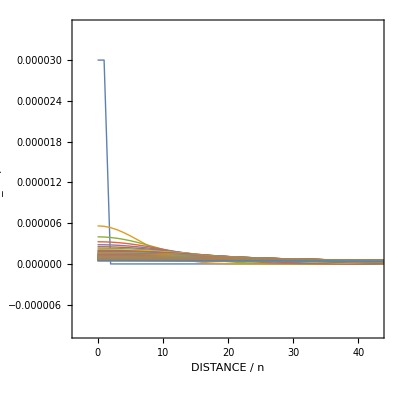

```mathematica
ListPlot[Table[{x, c[x, u]}, {u, 0, tmax, 50}, {x, 0, xmax}], Joined-> True, Frame-> True,PlotRange-> {{-3, 43}, {-0.00001, 0.000035}},BaseStyle->{16,FontFamily->"Helvetica"},LabelStyle->(FontFamily->"Helvetica"), AxesOrigin->{ -10, 0}, AspectRatio-> 1, PlotStyle->{Thick},FrameStyle->{Thick,Thick},FrameTicks-> {{0, 10, 20, 30, 40, 50},{0, 0.2, 0.4, 0.6, 0.8, 1},{},{}},FrameLabel->{"DISTANCE / n", "c_Ch / M"}]
```

```mathematica
c[1, 100]
```

```mathematica
dt
```

```mathematica
listc0=Table[{u dt, c[0, u]}, {u, 60, tmax}];
```

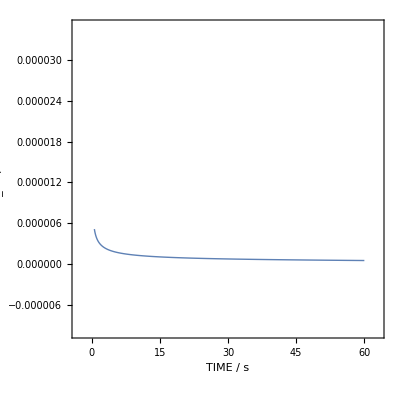

```mathematica
ListPlot[listc0, Joined-> True, Frame-> True,PlotRange-> {{-3, 63}, {-0.00001, 0.000035}},BaseStyle->{16,FontFamily->"Helvetica"},LabelStyle->(FontFamily->"Helvetica"), AxesOrigin->{ -10, 0}, AspectRatio-> 1, PlotStyle->{Thick},FrameStyle->{Thick,Thick},FrameTicks-> {{0, 10, 20, 30, 40, 50},{0, 0.2, 0.4, 0.6, 0.8, 1},{},{}},FrameLabel->{"TIME / s", "c_Ch / M"}]
```

## Equations for Diffusion Profile with Enzyme Kinetics

```mathematica
(cCh Vmax)/(cCh+KM)
```

## Parameters

```mathematica
n=.;
```

Distance steps in dm:

```mathematica
d= 5 10^-5;
```

Time steps in s:

```mathematica
dt= 0.01;
```

```mathematica
Da=10^-5 10^-2;
```

```mathematica
dtaua=Da dt/d^2
```

time in s :

```mathematica
tmax=60/dt
```

```mathematica
xmax=100;
```

```mathematica
Do[ce[x,t]=., {x, 0, xmax},{t, 0, tmax}];
```

```mathematica
Table[ce[x,t], {x, 0, xmax}, {t, 0, tmax}];
```

```mathematica
cbulk=0;
```

Initial concentrations:

```mathematica
Do[ce[x,0]=0.00003, {x, 0, 1}]
```

```mathematica
Do[ce[x,0]=0, {x, 2, xmax}]
```

```mathematica
Do[ce[xmax,t]=0, {t, 0, tmax}]
```

```mathematica
c[39,1]
```

## Calculation

```mathematica
For[t = 0, t < tmax, 
 
 {ce[0, t] = ce[0, t - 1] + dtaua (- 2 ce[0, t - 1] + 2ce[1, t - 1])-(ce[0, t - 1]  *2.3*10^-6)/(ce[0, t - 1] +0.2 10^-3),

  Do[ce[x, t] = ce[x, t - 1] + dtaua (ce[x - 1, t - 1] - 2 ce[x, t - 1] + ce[x + 1, t - 1]),
   {x, 1, xmax - 1}]
  
  }, 
 
 t++]
```

```mathematica
listce0=Table[{u dt, ce[0, u]}, {u, 60, tmax}];
```

```mathematica
c[1, 1]
```

One second is :

```mathematica
1/dt
```

100.

### Diffusion profile in the presence of enzyme-immunocomplex - concentration as a function of position

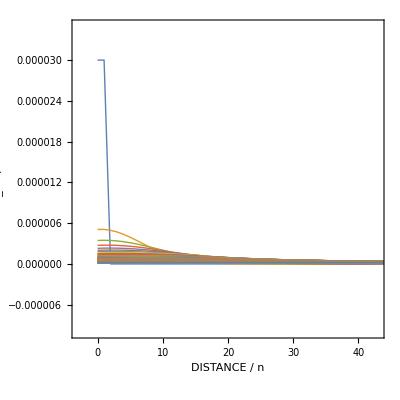

```mathematica
ListLinePlot[Table[{x, ce[x, u]}, {u, 0, tmax, 50}, {x, 0, xmax}], Joined-> True, Frame-> True,PlotRange-> {{-3, 43}, {-0.00001, 0.000035}},BaseStyle->{16,FontFamily->"Helvetica"},LabelStyle->(FontFamily->"Helvetica"), AxesOrigin->{ -10, 0}, AspectRatio-> 1, PlotStyle->{Thick},FrameStyle->{Thick,Thick},FrameTicks-> {{0, 10, 20, 30, 40, 50},{0, 0.2, 0.4, 0.6, 0.8, 1},{},{}},FrameLabel->{"DISTANCE / n", "c_Ch / M"}]
```

```mathematica
c[1, 100]
```

```mathematica
dt
```

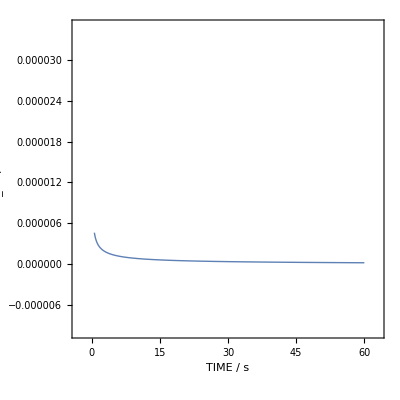

```mathematica
ListLinePlot[listce0,Frame-> True,PlotRange-> {{-3, 63}, {-0.00001, 0.000035}},BaseStyle->{16,FontFamily->"Helvetica"},LabelStyle->(FontFamily->"Helvetica"), AxesOrigin->{ -10, 0}, AspectRatio-> 1, PlotStyle->{Thick},FrameStyle->{Thick,Thick},FrameTicks-> {{0, 10, 20, 30, 40, 50},{0, 0.2, 0.4, 0.6, 0.8, 1},{},{}},FrameLabel->{"TIME / s", "c_Ch / M"}]
```

```mathematica
listce[[-1]]-listc0[[-1]]
```

### Potential measurement over time by inserting concentration at position zero in the Nernst equation in the absance and presence of enzyme-immunocomplex

```mathematica
Ec=Table[{u dt, 59.2 Log10[c[0, u]]}, {u, 60, tmax, 10}];
```

```mathematica
Ee=Table[{u dt, 59.2 Log10[ce[0, u]]}, {u, 60, tmax, 10}];

deltaE=Table[{u dt, 59.2 Log10[ce[0, u]]- 59.2 Log10[c[0, u]]}, {u, 60, tmax, 10}];
```

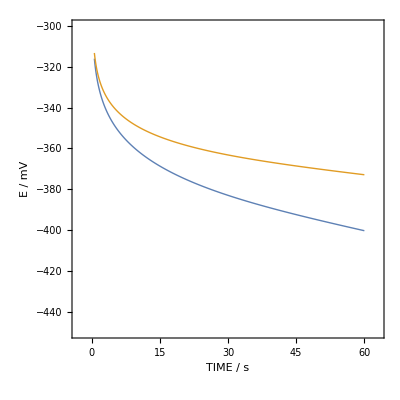

```mathematica
ListLinePlot[{Ee,Ec},

Frame-> True,PlotRange-> {{-3, 63}, {-300, -450}},BaseStyle->{16,FontFamily->"Helvetica"},LabelStyle->(FontFamily->"Helvetica"), AxesOrigin->{ -10, 0}, AspectRatio-> 1, PlotStyle->{Thick},FrameStyle->{Thick,Thick},FrameTicks-> {{0, 10, 20, 30, 40, 50},{0, 0.2, 0.4, 0.6, 0.8, 1},{},{}},FrameLabel->{"TIME / s", "E / mV"}]
```

### Potential change over time by subtracting the potential response in the absence of enzyme-immunocomplex from the potential measured in the presence of an enzyme-immunocomplex

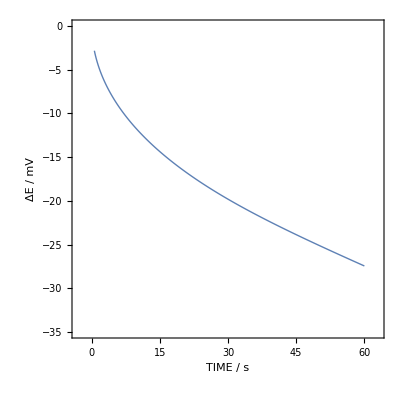

```mathematica
ListLinePlot[deltaE,

Frame-> True,PlotRange-> {{-3, 63}, {-35, 0}},BaseStyle->{16,FontFamily->"Helvetica"},LabelStyle->(FontFamily->"Helvetica"), AxesOrigin->{ -10, 0}, AspectRatio-> 1, PlotStyle->{Thick},FrameStyle->{Thick,Thick},FrameTicks-> {{0, 10, 20, 30, 40, 50},{0, 0.2, 0.4, 0.6, 0.8, 1},{},{}},FrameLabel->{"TIME / s", "ΔE / mV"}]
```